```mathematica
"definição do raio do circulo"
a=1
```

definição do raio do circulo

1

```mathematica
"definição do retângulo"
A=2a
B=2a
```

definição do retângulo

2

2

```mathematica
"definição da barreira de potencial Ka"
Ka=1000
```

definição da barreira de potencial Ka

1000

```mathematica
"definição da base harmonica e de seus autovalores"
φ[x_,y_,n_,m_]=2/(√(A*B))Sin[π*n(x/A)]Sin[π*m(y/B)]
nM=10
mM=10
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
κ[n_,m_]=π √((n/A)^2+(m/B)^2)
```

definição da base harmonica e de seus autovalores

Sin[(n π x)/2] Sin[(m π y)/2]

10

10

{Sin[(π x)/2] Sin[(π y)/2],Sin[π x] Sin[(π y)/2],Sin[(3 π x)/2] Sin[(π y)/2],Sin[2 π x] Sin[(π y)/2],Sin[(5 π x)/2] Sin[(π y)/2],Sin[3 π x] Sin[(π y)/2],Sin[(7 π x)/2] Sin[(π y)/2],Sin[4 π x] Sin[(π y)/2],Sin[(9 π x)/2] Sin[(π y)/2],Sin[5 π x] Sin[(π y)/2],Sin[(π x)/2] Sin[π y],Sin[π x] Sin[π y],Sin[(3 π x)/2] Sin[π y],Sin[2 π x] Sin[π y],Sin[(5 π x)/2] Sin[π y],Sin[3 π x] Sin[π y],Sin[(7 π x)/2] Sin[π y],Sin[4 π x] Sin[π y],Sin[(9 π x)/2] Sin[π y],Sin[5 π x] Sin[π y],Sin[(π x)/2] Sin[(3 π y)/2],Sin[π x] Sin[(3 π y)/2],Sin[(3 π x)/2] Sin[(3 π y)/2],Sin[2 π x] Sin[(3 π y)/2],Sin[(5 π x)/2] Sin[(3 π y)/2],Sin[3 π x] Sin[(3 π y)/2],Sin[(7 π x)/2] Sin[(3 π y)/2],Sin[4 π x] Sin[(3 π y)/2],Sin[(9 π x)/2] Sin[(3 π y)/2],Sin[5 π x] Sin[(3 π y)/2],Sin[(π x)/2] Sin[2 π y],Sin[π x] Sin[2 π y],Sin[(3 π x)/2] Sin[2 π y],Sin[2 π x] Sin[2 π y],Sin[(5 π x)/2] Sin[2 π y],Sin[3 π x] Sin[2 π y],Sin[(7 π x)/2] Sin[2 π y],Sin[4 π x] Sin[2 π y],Sin[(9 π x)/2] Sin[2 π y],Sin[5 π x] Sin[2 π y],Sin[(π x)/2] Sin[(5 π y)/2],Sin[π x] Sin[(5 π y)/2],Sin[(3 π x)/2] Sin[(5 π y)/2],Sin[2 π x] Sin[(5 π y)/2],Sin[(5 π x)/2] Sin[(5 π y)/2],Sin[3 π x] Sin[(5 π y)/2],Sin[(7 π x)/2] Sin[(5 π y)/2],Sin[4 π x] Sin[(5 π y)/2],Sin[(9 π x)/2] Sin[(5 π y)/2],Sin[5 π x] Sin[(5 π y)/2],Sin[(π x)/2] Sin[3 π y],Sin[π x] Sin[3 π y],Sin[(3 π x)/2] Sin[3 π y],Sin[2 π x] Sin[3 π y],Sin[(5 π x)/2] Sin[3 π y],Sin[3 π x] Sin[3 π y],Sin[(7 π x)/2] Sin[3 π y],Sin[4 π x] Sin[3 π y],Sin[(9 π x)/2] Sin[3 π y],Sin[5 π x] Sin[3 π y],Sin[(π x)/2] Sin[(7 π y)/2],Sin[π x] Sin[(7 π y)/2],Sin[(3 π x)/2] Sin[(7 π y)/2],Sin[2 π x] Sin[(7 π y)/2],Sin[(5 π x)/2] Sin[(7 π y)/2],Sin[3 π x] Sin[(7 π y)/2],Sin[(7 π x)/2] Sin[(7 π y)/2],Sin[4 π x] Sin[(7 π y)/2],Sin[(9 π x)/2] Sin[(7 π y)/2],Sin[5 π x] Sin[(7 π y)/2],Sin[(π x)/2] Sin[4 π y],Sin[π x] Sin[4 π y],Sin[(3 π x)/2] Sin[4 π y],Sin[2 π x] Sin[4 π y],Sin[(5 π x)/2] Sin[4 π y],Sin[3 π x] Sin[4 π y],Sin[(7 π x)/2] Sin[4 π y],Sin[4 π x] Sin[4 π y],Sin[(9 π x)/2] Sin[4 π y],Sin[5 π x] Sin[4 π y],Sin[(π x)/2] Sin[(9 π y)/2],Sin[π x] Sin[(9 π y)/2],Sin[(3 π x)/2] Sin[(9 π y)/2],Sin[2 π x] Sin[(9 π y)/2],Sin[(5 π x)/2] Sin[(9 π y)/2],Sin[3 π x] Sin[(9 π y)/2],Sin[(7 π x)/2] Sin[(9 π y)/2],Sin[4 π x] Sin[(9 π y)/2],Sin[(9 π x)/2] Sin[(9 π y)/2],Sin[5 π x] Sin[(9 π y)/2],Sin[(π x)/2] Sin[5 π y],Sin[π x] Sin[5 π y],Sin[(3 π x)/2] Sin[5 π y],Sin[2 π x] Sin[5 π y],Sin[(5 π x)/2] Sin[5 π y],Sin[3 π x] Sin[5 π y],Sin[(7 π x)/2] Sin[5 π y],Sin[4 π x] Sin[5 π y],Sin[(9 π x)/2] Sin[5 π y],Sin[5 π x] Sin[5 π y]}

√(m^2/4+n^2/4) π

```mathematica
"definição da matriz M que depende da barreira de potencial Ka"
M = Table[κ[1+Mod[j,nM],1+(j-Mod[j,nM])/mM]^2 KroneckerDelta[i,j]+ Ka^2NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,B},{x,0,a-√(y(2a-y))},AccuracyGoal->6]+Ka^2NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,B},{x,a+√(y(2a-y)),A},AccuracyGoal->6],{i,0,nM*mM-1},{j,0,nM*mM-1}] 
M // MatrixForm
```

definição da matriz M que depende da barreira de potencial Ka

{{6088.45,-2.72848×10^-12,13733.9,-1.81899×10^-12,13568.3,2.72848×10^-12,9864.68,-2.72848×10^-12,6615.09,1.81899×10^-12,7.92734×10^-12,-2.93907×10^-12,«77»,-4.09273×10^-12,-1.30179×10^-11,4.14954×10^-12,-3.34384×10^-11,1.21374×10^-12,-2.7848×10^-11,-3.73498×10^-12,1.75259×10^-11,-1.08139×10^-11,4.48311×10^-11,1.78306×10^-11},«98»,{«1»}}

(«1»)

```mathematica
"lista de autovalores e autofunções(para uma barreira Ka) da matriz M"
Lista = N[Eigensystem[M]]
```

lista de autovalores e autofunções(para uma barreira Ka) da matriz M

{{996473.,993747.,993747.,989591.,911082.,889119.,869559.,869558.,838912.,838911.,811347.,786823.,482414.,478990.,418815.,«71»,84.748,84.693,69.5595,65.6414,57.5166,57.2931,48.6889,48.5302,35.8228,31.1414,29.9308,17.5301,17.0591,6.80247},{«1»}}

```mathematica
"autofunção normalizada(para um dado autovalor k de indice id e barreira Ka) da matriz M"
id=nM*mM-4
ConsNorm =Lista[[2]][[id]].Lista[[2]][[id]]
ListaAutovalores2=Table[κ[1+Mod[i,nM],1+(i-Mod[i,nM])/mM]^2,{i,0,nM*mM-1}]
ListaCons2 = Table[(Lista[[2]][[id]][[1+i]])^2,{i,0,nM*mM-1}]
k=ListaAutovalores2.ListaCons2/ConsNorm
ϕ[x_,y_]=Base[x,y].Lista[[2]][[id]]/ConsNorm
```

autofunção normalizada(para um dado autovalor k de indice id e barreira Ka) da matriz M

96

1.

{π^2/2,(5 π^2)/4,(5 π^2)/2,(17 π^2)/4,(13 π^2)/2,(37 π^2)/4,(25 π^2)/2,(65 π^2)/4,(41 π^2)/2,(101 π^2)/4,(5 π^2)/4,2 π^2,(13 π^2)/4,5 π^2,(29 π^2)/4,10 π^2,(53 π^2)/4,17 π^2,(85 π^2)/4,26 π^2,(5 π^2)/2,(13 π^2)/4,(9 π^2)/2,(25 π^2)/4,(17 π^2)/2,(45 π^2)/4,(29 π^2)/2,(73 π^2)/4,(45 π^2)/2,(109 π^2)/4,(17 π^2)/4,5 π^2,(25 π^2)/4,8 π^2,(41 π^2)/4,13 π^2,(65 π^2)/4,20 π^2,(97 π^2)/4,29 π^2,(13 π^2)/2,(29 π^2)/4,(17 π^2)/2,(41 π^2)/4,(25 π^2)/2,(61 π^2)/4,(37 π^2)/2,(89 π^2)/4,(53 π^2)/2,(125 π^2)/4,(37 π^2)/4,10 π^2,(45 π^2)/4,13 π^2,(61 π^2)/4,18 π^2,(85 π^2)/4,25 π^2,(117 π^2)/4,34 π^2,(25 π^2)/2,(53 π^2)/4,(29 π^2)/2,(65 π^2)/4,(37 π^2)/2,(85 π^2)/4,(49 π^2)/2,(113 π^2)/4,(65 π^2)/2,(149 π^2)/4,(65 π^2)/4,17 π^2,(73 π^2)/4,20 π^2,(89 π^2)/4,25 π^2,(113 π^2)/4,32 π^2,(145 π^2)/4,41 π^2,(41 π^2)/2,(85 π^2)/4,(45 π^2)/2,(97 π^2)/4,(53 π^2)/2,(117 π^2)/4,(65 π^2)/2,(145 π^2)/4,(81 π^2)/2,(181 π^2)/4,(101 π^2)/4,26 π^2,(109 π^2)/4,29 π^2,(125 π^2)/4,34 π^2,(149 π^2)/4,41 π^2,(181 π^2)/4,50 π^2}

{1.11024×10^-6,8.52932×10^-25,0.445737,7.46005×10^-26,0.0423647,1.00231×10^-26,0.00488858,3.37627×10^-26,0.00101458,9.614×10^-28,6.99773×10^-28,3.66644×10^-24,1.99515×10^-28,7.75816×10^-25,3.23732×10^-28,8.81281×10^-27,7.23705×10^-29,5.33527×10^-29,1.3029×10^-30,4.66031×10^-28,0.452546,1.88674×10^-25,3.39333×10^-6,2.09424×10^-25,0.0000499605,3.32973×10^-27,0.00107651,3.71907×10^-27,0.00101433,7.21567×10^-29,2.74244×10^-27,7.39222×10^-25,1.58969×10^-27,1.84735×10^-27,2.30998×10^-27,5.2947×10^-26,1.74548×10^-28,7.68865×10^-28,2.60271×10^-30,8.14024×10^-29,0.0427296,2.59009×10^-25,0.0000514404,3.26162×10^-26,8.57338×10^-8,1.70299×10^-27,0.0000368615,4.42227×10^-28,0.000175721,6.24089×10^-29,1.30177×10^-27,3.45401×10^-27,2.95493×10^-27,3.24395×10^-26,2.33992×10^-27,1.1662×10^-29,7.40327×10^-31,1.68286×10^-27,4.69164×10^-29,5.11982×10^-28,0.00491076,8.47958×10^-28,0.00108081,1.51864×10^-26,0.0000388154,1.80628×10^-28,1.56891×10^-10,1.81411×10^-27,5.26169×10^-6,6.34674×10^-28,5.33545×10^-30,1.05301×10^-28,5.40878×10^-28,2.25068×10^-27,6.89756×10^-30,2.28755×10^-27,3.34092×10^-28,2.61587×10^-28,8.79257×10^-29,2.25153×10^-28,0.00104994,1.65457×10^-28,0.00103961,2.55491×10^-28,0.000178216,1.46903×10^-27,6.45746×10^-6,1.88564×10^-28,1.17701×10^-8,3.11178×10^-28,6.47013×10^-30,3.28895×10^-29,5.22924×10^-31,7.32362×10^-29,4.69451×10^-29,7.28188×10^-28,7.54936×10^-29,1.69997×10^-28,1.16272×10^-29,2.8493×10^-29}

30.1336

1. (-0.00105368 Sin[(π x)/2] Sin[(π y)/2]+9.23543×10^-13 Sin[π x] Sin[(π y)/2]-0.667635 Sin[(3 π x)/2] Sin[(π y)/2]-2.73131×10^-13 Sin[2 π x] Sin[(π y)/2]+0.205827 Sin[(5 π x)/2] Sin[(π y)/2]+1.00115×10^-13 Sin[3 π x] Sin[(π y)/2]+0.0699184 Sin[(7 π x)/2] Sin[(π y)/2]-1.83746×10^-13 Sin[4 π x] Sin[(π y)/2]+0.0318524 Sin[(9 π x)/2] Sin[(π y)/2]+3.10064×10^-14 Sin[5 π x] Sin[(π y)/2]+2.64532×10^-14 Sin[(π x)/2] Sin[π y]+1.91479×10^-12 Sin[π x] Sin[π y]-1.4125×10^-14 Sin[(3 π x)/2] Sin[π y]-8.80804×10^-13 Sin[2 π x] Sin[π y]+1.79926×10^-14 Sin[(5 π x)/2] Sin[π y]-9.38766×10^-14 Sin[3 π x] Sin[π y]-8.50708×10^-15 Sin[(7 π x)/2] Sin[π y]+7.3043×10^-15 Sin[4 π x] Sin[π y]-1.14145×10^-15 Sin[(9 π x)/2] Sin[π y]+2.15878×10^-14 Sin[5 π x] Sin[π y]+0.672716 Sin[(π x)/2] Sin[(3 π y)/2]+4.34367×10^-13 Sin[π x] Sin[(3 π y)/2]-0.0018421 Sin[(3 π x)/2] Sin[(3 π y)/2]-4.57629×10^-13 Sin[2 π x] Sin[(3 π y)/2]+0.00706827 Sin[(5 π x)/2] Sin[(3 π y)/2]+5.77038×10^-14 Sin[3 π x] Sin[(3 π y)/2]-0.0328102 Sin[(7 π x)/2] Sin[(3 π y)/2]+6.09842×10^-14 Sin[4 π x] Sin[(3 π y)/2]-0.0318485 Sin[(9 π x)/2] Sin[(3 π y)/2]-8.49451×10^-15 Sin[5 π x] Sin[(3 π y)/2]-5.23683×10^-14 Sin[(π x)/2] Sin[2 π y]-8.5978×10^-13 Sin[π x] Sin[2 π y]-3.98709×10^-14 Sin[(3 π x)/2] Sin[2 π y]+4.29808×10^-14 Sin[2 π x] Sin[2 π y]+4.80622×10^-14 Sin[(5 π x)/2] Sin[2 π y]+2.30102×10^-13 Sin[3 π x] Sin[2 π y]-1.32117×10^-14 Sin[(7 π x)/2] Sin[2 π y]+2.77284×10^-14 Sin[4 π x] Sin[2 π y]+1.61329×10^-15 Sin[(9 π x)/2] Sin[2 π y]-9.02233×10^-15 Sin[5 π x] Sin[2 π y]-0.206711 Sin[(π x)/2] Sin[(5 π y)/2]-5.0893×10^-13 Sin[π x] Sin[(5 π y)/2]-0.0071722 Sin[(3 π x)/2] Sin[(5 π y)/2]+1.806×10^-13 Sin[2 π x] Sin[(5 π y)/2]+0.000292803 Sin[(5 π x)/2] Sin[(5 π y)/2]+4.12673×10^-14 Sin[3 π x] Sin[(5 π y)/2]-0.00607136 Sin[(7 π x)/2] Sin[(5 π y)/2]+2.10292×10^-14 Sin[4 π x] Sin[(5 π y)/2]+0.013256 Sin[(9 π x)/2] Sin[(5 π y)/2]+7.89993×10^-15 Sin[5 π x] Sin[(5 π y)/2]+3.60801×10^-14 Sin[(π x)/2] Sin[3 π y]-5.87708×10^-14 Sin[π x] Sin[3 π y]+5.43593×10^-14 Sin[(3 π x)/2] Sin[3 π y]+1.8011×10^-13 Sin[2 π x] Sin[3 π y]-4.83728×10^-14 Sin[(5 π x)/2] Sin[3 π y]+3.41497×10^-15 Sin[3 π x] Sin[3 π y]-8.60423×10^-16 Sin[(7 π x)/2] Sin[3 π y]-4.10227×10^-14 Sin[4 π x] Sin[3 π y]+6.84956×10^-15 Sin[(9 π x)/2] Sin[3 π y]-2.2627×10^-14 Sin[5 π x] Sin[3 π y]-0.0700768 Sin[(π x)/2] Sin[(7 π y)/2]+2.91197×10^-14 Sin[π x] Sin[(7 π y)/2]+0.0328757 Sin[(3 π x)/2] Sin[(7 π y)/2]+1.23233×10^-13 Sin[2 π x] Sin[(7 π y)/2]+0.0062302 Sin[(5 π x)/2] Sin[(7 π y)/2]-1.34398×10^-14 Sin[3 π x] Sin[(7 π y)/2]+0.0000125256 Sin[(7 π x)/2] Sin[(7 π y)/2]-4.25923×10^-14 Sin[4 π x] Sin[(7 π y)/2]+0.00229384 Sin[(9 π x)/2] Sin[(7 π y)/2]-2.51927×10^-14 Sin[5 π x] Sin[(7 π y)/2]+2.30986×10^-15 Sin[(π x)/2] Sin[4 π y]-1.02616×10^-14 Sin[π x] Sin[4 π y]-2.32568×10^-14 Sin[(3 π x)/2] Sin[4 π y]+4.74413×10^-14 Sin[2 π x] Sin[4 π y]+2.62632×10^-15 Sin[(5 π x)/2] Sin[4 π y]-4.78283×10^-14 Sin[3 π x] Sin[4 π y]+1.82782×10^-14 Sin[(7 π x)/2] Sin[4 π y]-1.61736×10^-14 Sin[4 π x] Sin[4 π y]-9.37687×10^-15 Sin[(9 π x)/2] Sin[4 π y]+1.50051×10^-14 Sin[5 π x] Sin[4 π y]-0.0324028 Sin[(π x)/2] Sin[(9 π y)/2]+1.2863×10^-14 Sin[π x] Sin[(9 π y)/2]+0.032243 Sin[(3 π x)/2] Sin[(9 π y)/2]-1.59841×10^-14 Sin[2 π x] Sin[(9 π y)/2]-0.0133498 Sin[(5 π x)/2] Sin[(9 π y)/2]-3.8328×10^-14 Sin[3 π x] Sin[(9 π y)/2]-0.00254115 Sin[(7 π x)/2] Sin[(9 π y)/2]+1.37319×10^-14 Sin[4 π x] Sin[(9 π y)/2]+0.00010849 Sin[(9 π x)/2] Sin[(9 π y)/2]+1.76402×10^-14 Sin[5 π x] Sin[(9 π y)/2]-2.54365×10^-15 Sin[(π x)/2] Sin[5 π y]+5.73494×10^-15 Sin[π x] Sin[5 π y]+7.23135×10^-16 Sin[(3 π x)/2] Sin[5 π y]+8.55781×10^-15 Sin[2 π x] Sin[5 π y]+6.85165×10^-15 Sin[(5 π x)/2] Sin[5 π y]-2.6985×10^-14 Sin[3 π x] Sin[5 π y]-8.68871×10^-15 Sin[(7 π x)/2] Sin[5 π y]+1.30383×10^-14 Sin[4 π x] Sin[5 π y]+3.40987×10^-15 Sin[(9 π x)/2] Sin[5 π y]+5.33788×10^-15 Sin[5 π x] Sin[5 π y])

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(x-a)^2+(y-a)^2≤a^2]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

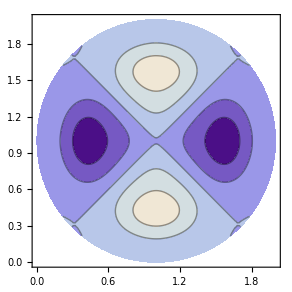

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(x-a)^2+(y-a)^2≤a^2]]
```